# 自编码器

help

## Intro

自编码器主要是将特征从原始输入层映射到隐层，再回到原始输出层，训练目标是度量输入层和输出层的损失。

从特征的角度来看，隐藏就相当于是一个特征变换

### 作用

获得隐藏的向量，用于降维
去噪

说一下降维呢，
在这个例子中，首先这里隐层降到了50维，DimensionReduce降到了2维或3维看起来效果超级好，特别是使用TSNE的时候，但是你不要以为自编码器有多么牛B，因为你可以做些实验，在原始图像特征中，TSNE+KMeans也有这里用的50维特征再降到2维的效果，说到底是降了两次，这是个有意思事情，之前我在另一个MNIST的实验中，也提到了这一点，降两次。

其次，说一下另一个问题，MNIST降维还有个example是TripletLoss做Embedding降到2维的，也可以找一下，是另一种方式。

其次，本例中，测试集使用的是自己的数据去降的维，如果要应用于预测场景，这是有问题的。
比如来一条样本，你没法降，当然这里只是一个降维的例子而已。

说一下去噪，得加点噪声呀，se上也有个帖子，本文就暂不贴了，因为我还没有仔细玩过，自己没玩过的不建议乱发不是，先这样。

## Net@Train

```mathematica
resource=ResourceObject["MNIST"];
trainingData=ResourceData[resource,"TrainingData"];
trainingSubset=Select[trainingData,Last[#]≤10&];
testData=ResourceData[resource,"TestData"];
testSubset=Select[testData,Last[#]≤10&];
RandomSample[trainingSubset,8]
```

{-Graphics-→0,-Graphics-→3,-Graphics-→2,-Graphics-→5,-Graphics-→4,-Graphics-→7,-Graphics-→8,-Graphics-→6}

```mathematica
trainingImages=Keys[trainingSubset];
meanImage=Image[Mean@Map[ImageData,trainingImages]]
```

-Graphics-

```mathematica
net=NetGraph[{FlattenLayer[],50,Ramp,784,Tanh,ReshapeLayer[{1,28,28}],MeanSquaredLossLayer[]},{1->2->3->4->5->6->NetPort["Output"],6->NetPort[7,"Input"],NetPort["Input"]->NetPort[7,"Target"]},"Input"->NetEncoder[{"Image",{28,28},"Grayscale","MeanImage"->meanImage}],
"Output"->NetDecoder[{"Image","Grayscale"}]]
```

NetGraph[]

NetGraph和NetChain的区别，主要是NetChain类似于一个链，比如在一个List里写所有的层，又如在Python里写一层一层的神经网络层，而当当看这些层，如果比较多，则不容易看出依赖关系，特别是有多个输入或输出的，这是Mathematica里定义网络看图的方便之处。

这个例子中有除了输出重构的图像外，还有输出第七层损失层。
一个更直观的例子是Cifar图像分类里同时训练大类和小类，MultiTask问题。

### CheckLoss

```mathematica
meanSquaredLoss=N[Mean[Flatten[(#Input-#Target)^2]]]&;
trained=NetTrain[net,<|"Input"->trainingImages|>,"Loss"];
```

{-Graphics-,<|Output→-Graphics-,Loss→0.00996173|>,-Graphics-}

```mathematica
res={#,trained@#,(trained@#)[[1]]}&@trainingImages[[1]]
```

{-Graphics-,<|Output→-Graphics-,Loss→0.00996173|>,-Graphics-}

```mathematica
{input=ImageSubtract[trainingImages[[1]],meanImage],out=res[[3]],diff=ImageSubtract[input,out]}
```

{-Graphics-,-Graphics-,-Graphics-}

可以看到，自己算的Loss跟网络计算的提取的结果是一样的

```mathematica
{Mean@((Flatten@ImageData@diff)^2),
loss=MeanSquaredLossLayer["Input"->{784}];
loss[<|"Input"->Flatten[ImageData@input],"Target"->Flatten[ImageData@out]|>]}
```

{0.00996173,0.00996173}

## 降维@可视化

```mathematica
reconstructor=Take[trained,{NetPort["Input"],NetPort["Output"]}]
```

NetGraph[]

```mathematica
rec=ImageAdd[reconstructor[#], meanImage] & /@trainingImages[[1;;5]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
encoder=Take[trained,{NetPort["Input"],4}]
```

NetGraph[]

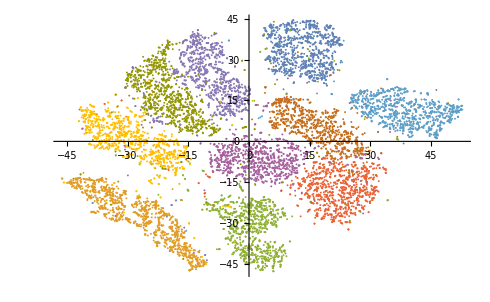

```mathematica
testImages=Keys[testSubset];
features=encoder[testImages];
classes=Values[testSubset];
coords2D=DimensionReduce[features,2,Method->"TSNE"];
data2D=Table[Extract[coords2D,Position[classes,i]],{i,0,9}];
ListPlot[data2D]
```

#### TSNE直接从784维向量聚类的效果

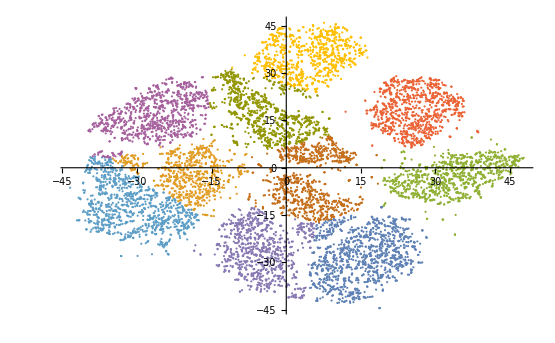

```mathematica
(*coords3D=DimensionReduce[features,3,Method->"TSNE"];*)
```

```mathematica
(*data3D=Table[Extract[coords3D,Position[classes,i]],{i,0,4}];*)
```

```mathematica
(*ListPointPlot3D[data3D,PlotLegends->PointLegend[96,Range[0,4]],BoxRatios->1,Axes->None,Boxed->True,PlotStyle->Map[ColorData[96],Range[1,5]],AspectRatio->1]*)
```

## Refs

question

GitHub/MNIST/Clustering@MNIST

GitHub/MNIST/AutoEncoder@Note

## 小结

遇到的问题：11.2最多的就是卡住半天没反应，前端Dynamic错误啥的，资源下载慢啥的。
如果遇到大段代码半天没反应，就使用单元分割快捷键，分割多行代码运行。

TNSE比较慢，降到2维比较快，效果确实好。

## 其他

Tools文件夹中的MyMarkDown.md已经具有一定的易用性，大家看我的知乎的文章，即是Mathematica写作，一个命令导出，然后再粘贴到专栏。
推广一下，有人使用的话可以提一些需求。

```mathematica
<<"/Users/hypergroups/Documents/Wolfram Mathematica/DeployProjects/MyMarkDown.m"
```

```mathematica
Notebook2Markdown[EvaluationNotebook[],"title"->"AutoEncoder","dirOutput"->"/Users/hypergroups/Documents/MyMarkdown/知乎专栏/"]
```

{fileExport= /Users/hypergroups/Documents/MyMarkdown/知乎专栏/AutoEncoder/resource/AutoEncoder_14.jpg,AutoEncoder/resource/AutoEncoder_14.jpg fileExportRelative=}

{fileExport= /Users/hypergroups/Documents/MyMarkdown/知乎专栏/AutoEncoder/resource/AutoEncoder_16.jpg,AutoEncoder/resource/AutoEncoder_16.jpg fileExportRelative=}

{fileExport= /Users/hypergroups/Documents/MyMarkdown/知乎专栏/AutoEncoder/resource/AutoEncoder_18.jpg,AutoEncoder/resource/AutoEncoder_18.jpg fileExportRelative=}

{fileExport= /Users/hypergroups/Documents/MyMarkdown/知乎专栏/AutoEncoder/resource/AutoEncoder_23.jpg,AutoEncoder/resource/AutoEncoder_23.jpg fileExportRelative=}

{fileExport= /Users/hypergroups/Documents/MyMarkdown/知乎专栏/AutoEncoder/resource/AutoEncoder_25.jpg,AutoEncoder/resource/AutoEncoder_25.jpg fileExportRelative=}

{fileExport= /Users/hypergroups/Documents/MyMarkdown/知乎专栏/AutoEncoder/resource/AutoEncoder_27.jpg,AutoEncoder/resource/AutoEncoder_27.jpg fileExportRelative=}

RawString

{fileExport= /Users/hypergroups/Documents/MyMarkdown/知乎专栏/AutoEncoder/resource/AutoEncoder_33.jpg,AutoEncoder/resource/AutoEncoder_33.jpg fileExportRelative=}

{fileExport= /Users/hypergroups/Documents/MyMarkdown/知乎专栏/AutoEncoder/resource/AutoEncoder_35.jpg,AutoEncoder/resource/AutoEncoder_35.jpg fileExportRelative=}

{fileExport= /Users/hypergroups/Documents/MyMarkdown/知乎专栏/AutoEncoder/resource/AutoEncoder_37.jpg,AutoEncoder/resource/AutoEncoder_37.jpg fileExportRelative=}

{fileExport= /Users/hypergroups/Documents/MyMarkdown/知乎专栏/AutoEncoder/resource/AutoEncoder_39.jpg,AutoEncoder/resource/AutoEncoder_39.jpg fileExportRelative=}

{fileExport= /Users/hypergroups/Documents/MyMarkdown/知乎专栏/AutoEncoder/resource/AutoEncoder_41.jpg,AutoEncoder/resource/AutoEncoder_41.jpg fileExportRelative=}

```mathematica
NotebookDirectory[]
```

/Users/hypergroups/Documents/Wolfram Mathematica/知乎专栏/